### Running

```mathematica
resall = ;
```

#### Outtake

```mathematica
ListLogLogPlot[Join[KeyValueMap[Callout[#2,GraphicsColumn[{CellularAutomatonHistoryPlot["GameOfLife", {$LifeData[#1]["MatrixData"], 0}, 5,ImageSize->{100,100}],Text[Style[$LifeData[#1]["Year"],8]]}, ImageSize->30]]&,#1],Values[#2]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@Association[resall]]]],None]],60]]
```

-Graphics-

Make year visible

```mathematica
ListLogLogPlot[Join[KeyValueMap[Callout[#2,GraphicsColumn[{CellularAutomatonHistoryPlot["GameOfLife", {$LifeData[#1]["MatrixData"], 0}, 5,ImageSize->{200,200}],Text[Style[$LifeData[#1]["Year"],8]]}, Spacings->10]]&,#1],Values[#2]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@Association[resall]]]],None]],60]]
```

-Graphics-

#### Run the year axis down....

```mathematica
ListPlot[KeyValueMap[Callout[#2,CellularAutomatonHistoryPlot["GameOfLife", {$LifeData[#1]["MatrixData"], 0}, 5,ImageSize->{100,100}],Top]&,Association[#1]]&@KeyValueMap[#1->$LifeData[#1]["Year"]&,ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@Association[resall]]]],None]]],PlotRange->{{0,40},Automatic},AspectRatio->.4,Frame->True,FrameLabel->{"rank","year"}]
```

-Graphics-

```mathematica
ListPlot[KeyValueMap[Callout[#2,CellularAutomatonHistoryPlot["GameOfLife", {$LifeData[#1]["MatrixData"], 0}, 5,ImageSize->{20, 20}(*10Times@@Dimensions[$LifeData[#1]["MatrixData"]]^.2*), MeshStyle->Opacity[.05]],(*If[#2 <2010, *)Bottom(*, Top]*)]&,Association[#1]]&@KeyValueMap[#1->$LifeData[#1]["Year"]&,Take[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@Association[resall]]]],None]], 40]],PlotRange->{{0,41},{1965, 2030}},AspectRatio->.4,Frame->True,FrameLabel->{"rank","year"}, ScalingFunctions->"Reverse", PlotRangePadding->{{Automatic, None},{1.55, None}}, PlotStyle->PointSize[.0075]]
```

-Graphics-

#### To be debugged

```mathematica
activity = Module[{rrr, xr},
rrr=Association[DeleteCases[Union[#],None]&/@Association[resall]];
xr=Flatten[KeyValueMap[Thread[#2->$LifeData[#1]["Year"]]&,Association[rrr]]];
#->Cases[xr,(#->x_)->x]&/@Keys[Take[ReverseSort[Counts[Flatten[Values[rrr]]]],20]]];
```

Number lines:

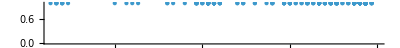
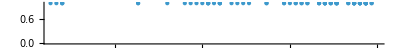
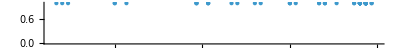
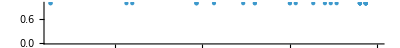
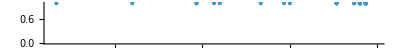
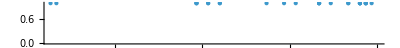
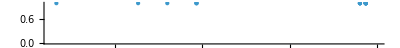
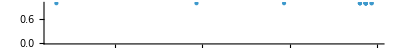
-Graphics-Block
-Graphics-Glider
-Graphics-Tub
-Graphics-Blinker
-Graphics-Figure eight
-Graphics-Beehive
-Graphics-Toad
-Graphics-Clock
-Graphics-Pentadecathlon
-Graphics-Unix

```mathematica
Column[KeyValueMap[Labeled[NumberLinePlot[#2, PlotRange->{1969, 2025}], Text[#1], Top]&, Take[Association[activity], 10]], Frame->All]
```

BarChart:

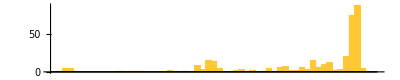
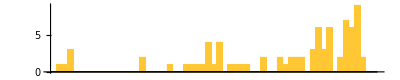
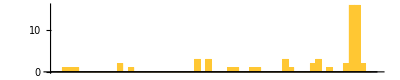
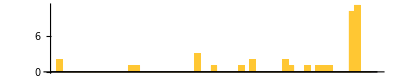
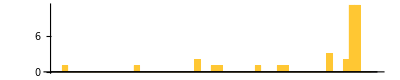
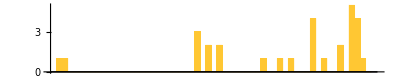
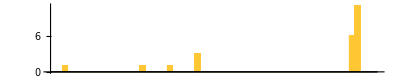
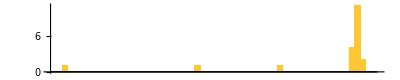
-Graphics-Block
-Graphics-Glider
-Graphics-Tub
-Graphics-Blinker
-Graphics-Figure eight
-Graphics-Beehive
-Graphics-Toad
-Graphics-Clock

```mathematica
Column[KeyValueMap[Labeled[BarChart[Table[Lookup[#2, i, 0], {i, 1969, 2025}], AspectRatio->.2], Text[#1], Top]&,Counts/@Take[Association[activity], 8]], Frame->All]
```

```mathematica
BarChart[KeyValueMap[Table[Lookup[#2, i, 0], {i, 1969, 2025}]&, Counts/@Take[Association[activity], 12]], ChartLayout->{"Row", UpTo[4]}, ChartLabels->(List[Style[#, 12]]&)/@Keys[Counts/@Take[Association[activity], 12]], ScalingFunctions->"Log"(*, Ticks-> {With[{r = Range[1969, 2025]}, Table[Reverse@{i, r[[i]]}, {i, 1,2025 - 1969 + 1}]], Automatic}*)]
```

-Graphics-

```mathematica
f[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:={Rectangle[{xmin,ymin},{xmax,ymax}]}
```

```mathematica
g[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:=Polygon[{{xmin,ymin},{xmax,ymax},{xmin,ymax},{xmax,ymin}}]
```

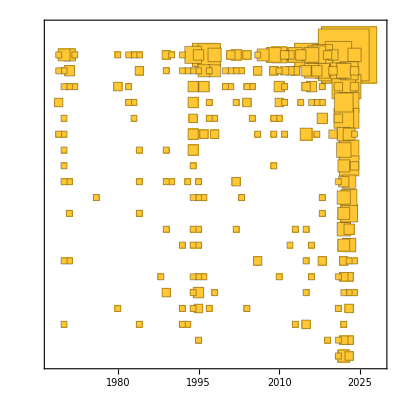

```mathematica
BubbleChart[Catenate[MapIndexed[Function[{assoc, idx}, KeyValueMap[{#1, First@idx, #2}&,assoc]], Values[Counts/@Take[Association[activity], 20]]]], ChartElementFunction->f, ScalingFunctions->{Automatic, "Reverse"}, PlotRangePadding->{{None, None}, {Automatic, .25}}, FrameTicks-> {{Transpose[{Range[1, 20,1], CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},10,ImageSize->{20,20}, MeshStyle->Opacity[.05]]&/@Keys[Take[Association[activity], 20]]}], Automatic}, {Automatic, Automatic}} ]
```

LinePlot

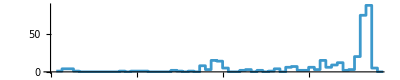
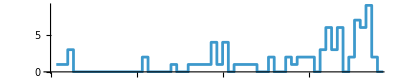
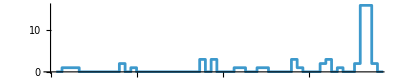
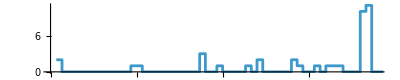
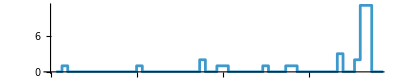
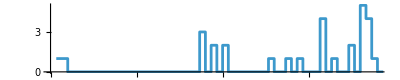
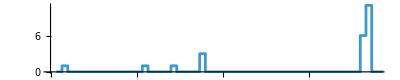
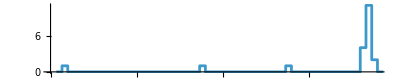
-Graphics-Block
-Graphics-Glider
-Graphics-Tub
-Graphics-Blinker
-Graphics-Figure eight
-Graphics-Beehive
-Graphics-Toad
-Graphics-Clock

```mathematica
Column[KeyValueMap[Labeled[ListStepPlot[Table[Lookup[#2, i, 0], {i, 1969, 2025}], AspectRatio->.2, PlotRange->All, PlotTheme->"Minimal"], Text[#1], Top]&,Counts/@Take[Association[activity], 8]], Frame->All]
```

#### Flip this around for “Euclid style”

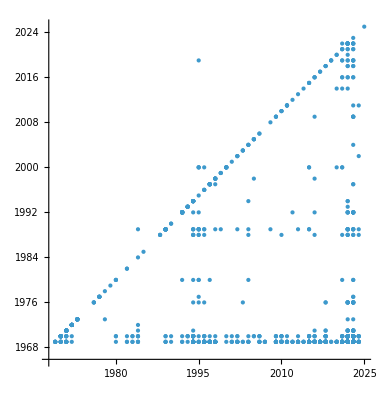

```mathematica
ListPlot[{$LifeData[#1]["Year"],$LifeData[#2]["Year"]}&@@@Flatten[Thread/@Normal[DeleteCases[None]/@resall]],AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[Large]]
```

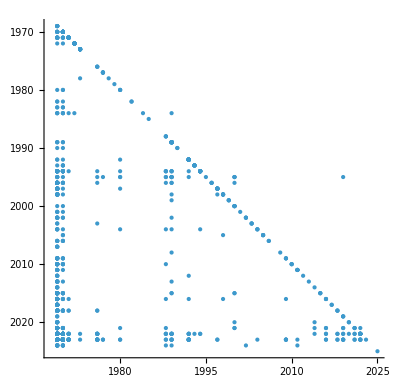

```mathematica
ListPlot[{$LifeData[#2]["Year"],$LifeData[#1]["Year"]}&@@@Flatten[Thread/@Normal[DeleteCases[None]/@resall]],AspectRatio->Automatic,PlotRange->All,PlotStyle->PointSize[Large], ScalingFunctions->"Reverse"]
```

#### Why is the spaceship different?

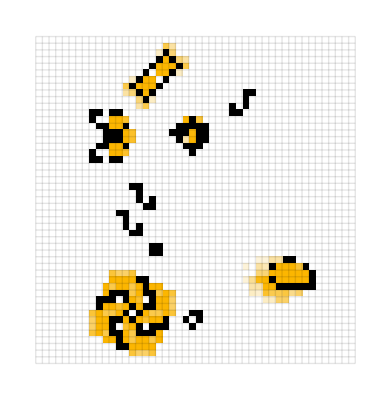

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {SparseArray[…], 0}, {8,Automatic,{-5,40}}]
```

```mathematica
With[{ca=Drop[PatternElements[Normal[SparseArray[…]]],-2]},KeyValueMap[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#,0},0,ImageSize->50],Text[StringJoin[ToString[#2],"×"]],Top]&,ca]]
```

{-Graphics-3×,-Graphics-1×,-Graphics-1×,-Graphics-1×,-Graphics-1×,-Graphics-1×,-Graphics-1×,-Graphics-1×}

It’s because the morphological components pulls it apart

```mathematica
ArrayPlot[MorphologicalComponents[SparseArray[…]], ImageSize->100] // Colorize
```

-Graphics-

This is what you want to do

#### Dev

```mathematica
SparseArray[…]["ExplicitPositions"]
```

```mathematica
ArrayPlot[SparseArray[Thread[CanonicalIdxs[#]->1]], ImageSize->50]&/@ CausalSeparation[SparseArray[#]["ExplicitPositions"]]&/@ CellularAutomaton["GameOfLife", {SparseArray[…], 0}, 10]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[SparseArray[Thread[CanonicalIdxs[#]->1]], ImageSize->50]&/@ CausalSeparation[SparseArray[…]["ExplicitPositions"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Final

```mathematica
GraphicsRow[KeyValueMap[Labeled[ArrayPlot[SparseArray[Thread[#1->1]], ImageSize->50], Text[ToString[#2]<>"x"], Top]&, Counts[CanonicalIdxs/@
CausalSeparation[SparseArray[…]["ExplicitPositions"]]]], Spacings-> 15]
```

-Graphics-

May need to pick a separate one because these are all separated

### Variance of distribution of the parts (measure of invented or discovered)

#### Dev

```mathematica
Kurtosis@RandomVariate[UniformDistribution[{1, 1.1}], 10]
```

2.78891

```mathematica
Kurtosis[Table[]]
```

```mathematica
Kurtosis[Table[1, 10]]
```

Indeterminate

```mathematica
Skewness[Table[1, 10]]
```

Indeterminate

```mathematica
Kurtosis[{1, 1, 1, 2, 1, 1 }]
```

21/5

```mathematica
Kurtosis[{1, 1, 2, 1, 1 }]
```

```mathematica
Variance[{1, 1, 1, 2, 1, 1 }]
```

1/6

```mathematica
Variance[{0,0,3,1,1}]
```

3/2

```mathematica
Variance[{5, 0, 0, 0 , 0}]
```

5

```mathematica
Variance[{8, 1, 1, 1}] // N
```

12.25

```mathematica
Variance/@
```

```mathematica
byyear = SortBy[Select[$LifeData, Times@@Dimensions[#MatrixData] <3000&], #Year&];
```

```mathematica
seps = CausalSeparation[#MatrixData["ExplicitPositions"]]&/@ SortBy[Select[$LifeData, #Class === "Oscillator" && Times@@Dimensions[#MatrixData] <3000&], #Year&];
```

```mathematica
N@Variance[{1, 1000, 5, 1}]
```

248838.

```mathematica
Length[Select[$LifeData, #Class === "Oscillator"&]]
```

775

```mathematica
Length[seps]
```

700

```mathematica
cs =  Counts[CanonicalIdxs/@#]&/@ seps;
```

```mathematica
ks = Kurtosis/@Values/@Select[cs, Length[#]>1&];
```

```mathematica
vs = Variance/@Values/@Select[cs, Length[#]>1&];
```

```mathematica
Length[byyear]
```

700

#### Running just oscillators

```mathematica
seps = CausalSeparation[#MatrixData["ExplicitPositions"]]&/@ SortBy[Select[$LifeData, #Class === "Oscillator" && Times@@Dimensions[#MatrixData] <3000&], #Year&];
cs =  Counts[CanonicalIdxs/@#]&/@ seps;
vs = Variance/@Values/@Select[cs, Length[#]>1&];
```

```mathematica
BarChart[KeyValueMap[If[#2>10, Callout[#2, $LifeData[#1]["Year"]], #2]&, vs], Frame-> True,FrameTicks-> {{True, False}, {False, False}}, FrameLabel->Reverse@{"constructedness", "time"}]
```

-Graphics-

```mathematica
ListPlot[KeyValueMap[Callout[#2,#1]&,vs], PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[$LifeData["Gallus"]["MatrixData"]]
```

-Graphics-

```mathematica
ArrayPlot[$LifeData["128P10.2"]["MatrixData"]]
```

-Graphics-

#### Running all

```mathematica
seps = CausalSeparation[#MatrixData["ExplicitPositions"]]&/@ SortBy[Select[$LifeData, Times@@Dimensions[#MatrixData] <3000&], #Year&];
```

```mathematica
cs =  Counts[CanonicalIdxs/@#]&/@ seps;
```

```mathematica
vs = Variance/@Values/@Select[cs, Length[#]>1&];
```

```mathematica
ListPlot[Association[KeyValueMap[#1->{$LifeData[#1]["Year"], #2}&, vs]], PlotRange->All]
```

-Graphics-

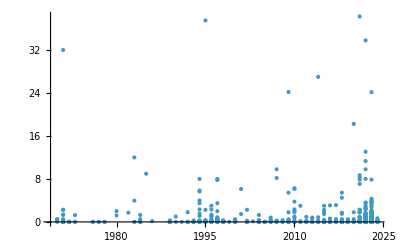

```mathematica
ListPlot[Values[Association[KeyValueMap[#1->{$LifeData[#1]["Year"], #2}&, vs]]], PlotRange->All, PlotHighlighting->None]
```

High constructedness guys:

```mathematica
Labeled[ArrayPlot[$LifeData[#]["MatrixData"], ImageSize->100],Text[$LifeData[#]["Year"]]]&/@Keys[TakeLargest[vs, 30]]
```

{-Graphics-2021,-Graphics-1995,-Graphics-2022,-Graphics-1971,-Graphics-2014,-Graphics-2009,-Graphics-2023,-Graphics-2020,-Graphics-2022,-Graphics-1983,-Graphics-2022,-Graphics-2007,-Graphics-2022,-Graphics-1985,-Graphics-2021,-Graphics-2021,-Graphics-2007,-Graphics-1994,-Graphics-1997,-Graphics-2022,-Graphics-2021,-Graphics-2023,-Graphics-1997,-Graphics-2021,-Graphics-2010,-Graphics-2001,-Graphics-2010,-Graphics-1994,-Graphics-1994,-Graphics-2009}

Distribution of parts

```mathematica
BarChart[#, ImageSize->100]&/@ (cs[#]&)/@ Keys[TakeLargest[vs, 30]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Low variance (low constructedness)

```mathematica
ArrayPlot[$LifeData[#]["MatrixData"], ImageSize->100]&/@Keys[TakeSmallest[vs, 30]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BarChart[#, ImageSize->100]&/@ (cs[#]&)/@ Keys[TakeSmallest[vs, 30]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Adding the arrow technology in